```mathematica
A =   
{{8, 1, 11},
{4, 0, 4}, 
{-4, -3, -7}};

B = 
{{-1}, {-3}, {3}};

x0={1,1,1};

alpha1 = 0.5; alpha2 = 3;
nu = 1; R = {{1}};
```

```mathematica
sys=StateSpaceModel[{A,B}];
U = ControllabilityMatrix[sys];
MatrixRank[U];
```

```mathematica
{vals,vecs}=Eigensystem[A]; v=vecs[[2]];
Pj=Transpose[{vecs[[1]],Re[v],Im[v]}];

Aj = Simplify[Inverse[Pj].A.Pj];
Bj = Inverse[Pj].B;
```

```mathematica
(*альфа1 = 0.5, регулятор К1, Ляпунов*)

hatKa1K1L = {{0, 1.69, 2.63}};
Ka1K1L = hatKa1K1L.Inverse[Pj];
Acla1K1L = A + B.Ka1K1L;
Eigenvalues[Acla1K1L];
```

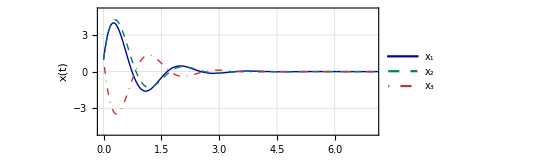

```mathematica
xa1K1L[t_]:=MatrixExp[Acla1K1L t].x0;

Xa1K1L=Plot[Evaluate[xa1K1L[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.02,7},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa1K1L.pdf"}],Xa1K1L];
```

```mathematica
(*альфа1 = 0.5, регулятор К2, Ляпунов*)

hatKa1K2L = {{0, 0.99, 1.85}};
Ka1K2L = hatKa1K2L.Inverse[Pj];
Acla1K2L = A + B.Ka1K2L;
Eigenvalues[Acla1K2L];
```

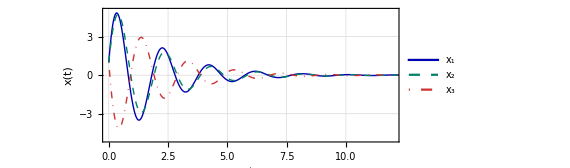

```mathematica
xa1K2L[t_]:=MatrixExp[Acla1K2L t].x0;

Xa1K2L=Plot[Evaluate[xa1K2L[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.02,12},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa1K2L.pdf"}],Xa1K2L];
```

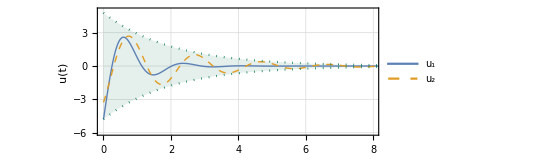

```mathematica
(*альфа1 = 0.5, управления, Ляпунов*)

ua1k1L[t_]:=(Ka1K1L.xa1K1L[t])[[1]];
ua1k2L[t_]:=(Ka1K2L.xa1K2L[t])[[1]];
c= 4.79;

Ua1L=Plot[{ua1k1L[t],ua1k2L[t],c Exp[-0.5 t],-c Exp[-0.5 t]},{t,0,20},PlotRange->{{-0.02,8},{-6,5}},PlotStyle->{{SilverColor,Thick},{GoldenrodYellow,Dashed,Thick}, {RGBColor[0.0,0.45,0.3], Dotted}, {RGBColor[0.0,0.45,0.3], Dotted}},
Filling->{3->{4}},FillingStyle->Directive[RGBColor[0.0,0.45,0.3],Opacity[0.1]],
PlotLegends->Placed[LineLegend[{Subscript[u,1],Subscript[u,2]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.75,0.9}],Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Ua1L.pdf"}],Ua1L];
```

```mathematica
(*альфа2 = 3, регулятор К1, Ляпунов*)

hatKa2K1L = {{0, 8.4439, 7.4628}};
Ka2K1L = hatKa2K1L.Inverse[Pj];
Acla2K1L = A + B.Ka2K1L;
Eigenvalues[Acla2K1L];
```

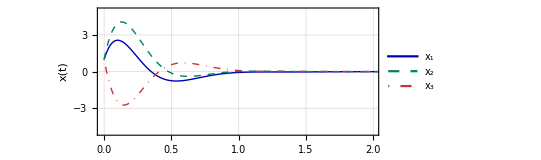

```mathematica
xa2K1L[t_]:=MatrixExp[Acla2K1L t].x0;

Xa2K1L=Plot[Evaluate[xa2K1L[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.01,2},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa2K1L.pdf"}],Xa2K1L];
```

```mathematica
(*альфа2 = 3, регулятор К2, Ляпунов*)

hatKa2K2L = {{0, 5, 5}};
Ka2K2L = hatKa2K2L.Inverse[Pj];
Acla2K2L = A + B.Ka2K2L;
Eigenvalues[Acla2K2L];
```

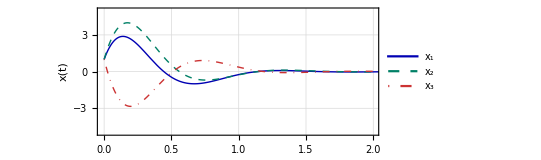

```mathematica
xa2K2L[t_]:=MatrixExp[Acla2K2L t].x0;

Xa2K2L=Plot[Evaluate[xa2K2L[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.01,2},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa2K2L.pdf"}],Xa2K2L];
```

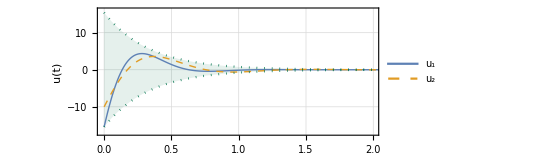

```mathematica
(*альфа2 = 3, управления, Ляпунов*)

ua2k1L[t_]:=(Ka2K1L.xa2K1L[t])[[1]];
ua2k2L[t_]:=(Ka2K2L.xa2K2L[t])[[1]];
c= 15.4161499;

Ua2L=Plot[{ua2k1L[t],ua2k2L[t],c Exp[-3t],-c Exp[-3t]},{t,0,20},PlotRange->{{-0.01,2.},{-17,16}},PlotStyle->{{SilverColor,Thick},{GoldenrodYellow,Dashed,Thick}, {RGBColor[0.0,0.45,0.3], Dotted}, {RGBColor[0.0,0.45,0.3], Dotted}},
Filling->{3->{4}},FillingStyle->Directive[RGBColor[0.0,0.45,0.3],Opacity[0.1]],
PlotLegends->Placed[LineLegend[{Subscript[u,1],Subscript[u,2]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.75,0.9}],Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Ua2L.pdf"}],Ua2L];
```

```mathematica
(*альфа1 = 0.5, регулятор при Q == I, Риккати*)

QI=IdentityMatrix[3];
tildeAa1Q1R=A+alpha1 IdentityMatrix[3];
Pa1Q1R=RiccatiSolve[{tildeAa1Q1R,B},{QI,R/nu}];
Ka1Q1R=-Inverse[R].Transpose[B].Pa1Q1R;

Acla1Q1R = A + B.Ka1Q1R;
Eigenvalues[Acla1Q1R]
```

{-5.66551+3.86426 ⅈ,-5.66551-3.86426 ⅈ,-3.+0. ⅈ}

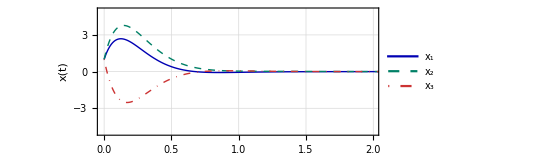

```mathematica
xa1Q1R[t_]:=MatrixExp[Acla1Q1R t].x0;

Xa1Q1R=Plot[Evaluate[xa1Q1R[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.01,2},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa1Q1R.pdf"}],Xa1Q1R];
```

```mathematica
(*альфа1 = 3, регулятор при Q == 0, Риккати*)

Q0={{0,0,0},{0,0,0},{0,0,0}};
tildeAa1Q0R=A+alpha1 IdentityMatrix[3];
Pa1Q0R=RiccatiSolve[{tildeAa1Q0R,B},{Q0,R/nu}];
Ka1Q0R=-Inverse[R].Transpose[B].Pa1Q0R;

Acla1Q0R = A + B.Ka1Q0R;
Eigenvalues[Acla1Q0R]
```

{-3.+2. ⅈ,-3.-2. ⅈ,-3.+0. ⅈ}

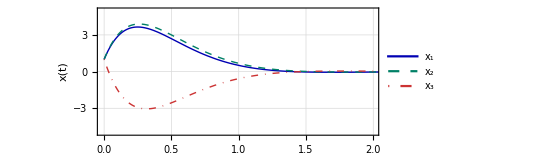

```mathematica
xa1Q0R[t_]:=MatrixExp[Acla1Q0R t].x0;

Xa1Q0R=Plot[Evaluate[xa1Q0R[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.01,2},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa1Q0R.pdf"}],Xa1Q0R];
```

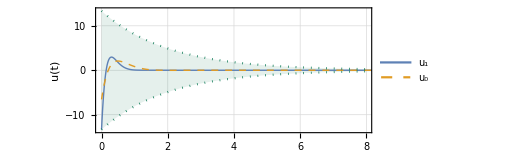

```mathematica
(*альфа1 = 0.5, управления, Риккати*)

ua1Q1R[t_]:=(Ka1Q1R.xa1Q1R[t])[[1]];
ua1Q0R[t_]:=(Ka1Q0R.xa1Q0R[t])[[1]];
c= ua1Q1R[0];

Ua1R=Plot[{ua1Q1R[t],ua1Q0R[t],c Exp[-alpha1 t],-c Exp[-alpha1 t]},{t,0,20},PlotRange->{{-0.02,8},{-13.5,13.5}},PlotStyle->{{SilverColor,Thick},{GoldenrodYellow,Dashed,Thick}, {RGBColor[0.0,0.45,0.3], Dotted}, {RGBColor[0.0,0.45,0.3], Dotted}},
Filling->{3->{4}},FillingStyle->Directive[RGBColor[0.0,0.45,0.3],Opacity[0.1]],
PlotLegends->Placed[LineLegend[{Subscript[u,1],Subscript[u,0]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.75,0.9}],Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Ua1R.pdf"}],Ua1R];
```

```mathematica
(*альфа2 = 2.99, регулятор при Q == I, Риккати*)
alpha2 = 2.9;
QI={{1,0,0},{0,1,0},{0,0,1}};
tildeAa2Q1R=A+alpha2 IdentityMatrix[3];
Pa2Q1R=RiccatiSolve[{tildeAa2Q1R,B},{QI,R/nu}];
Ka2Q1R=-Inverse[R].Transpose[B].Pa2Q1R;

Acla2Q1R = A + B.Ka2Q1R;
Eigenvalues[Acla2Q1R];
```

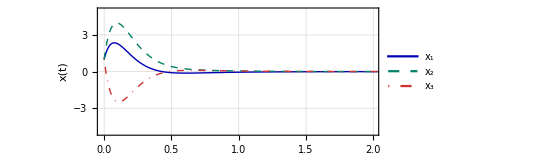

```mathematica
xa2Q1R[t_]:=MatrixExp[Acla2Q1R t].x0;

Xa2Q1R=Plot[Evaluate[xa2Q1R[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.01,2},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa2Q1R.pdf"}],Xa2Q1R];
```

```mathematica
(*альфа2 = 2.99, регулятор при Q == 0, Риккати*)
alpha2 = 2.9;
QI={{0,0,0},{0,0,0},{0,0,0}};
tildeAa2Q0R=A+alpha2 IdentityMatrix[3];
Pa2Q0R=RiccatiSolve[{tildeAa2Q0R,B},{QI,R/nu}];
Ka2Q0R=-Inverse[R].Transpose[B].Pa2Q0R

Acla2Q0R = A + B.Ka2Q0R;
Eigenvalues[Acla2Q0R]
```

{{-9.69862,0.0675862,-9.69862}}

{-7.8+2. ⅈ,-7.8-2. ⅈ,-3.+0. ⅈ}

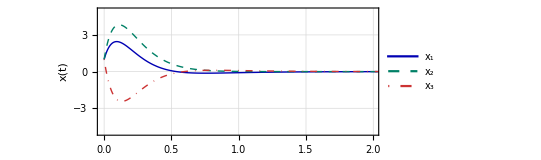

```mathematica
xa2Q0R[t_]:=MatrixExp[Acla2Q0R t].x0;

Xa2Q0R=Plot[Evaluate[xa2Q0R[t]],{t,0,20},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.01,2},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Xa2Q0R.pdf"}],Xa2Q0R];
```

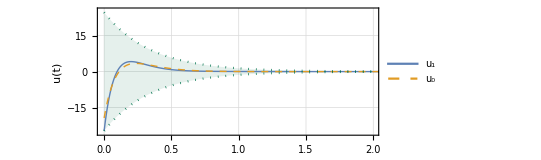

```mathematica
(*альфа2 = 3, управления, Риккати*)

ua2Q1R[t_]:=(Ka2Q1R.xa2Q1R[t])[[1]];
ua2Q0R[t_]:=(Ka2Q0R.xa2Q0R[t])[[1]];
c= ua2Q1R[0];

Ua2R=Plot[{ua2Q1R[t],ua2Q0R[t],c Exp[-alpha2 t],-c Exp[-alpha2 t]},{t,0,20},PlotRange->{{-0.01,2},{-25.5,25.5}},PlotStyle->{{SilverColor,Thick},{GoldenrodYellow,Dashed,Thick}, {RGBColor[0.0,0.45,0.3], Dotted}, {RGBColor[0.0,0.45,0.3], Dotted}},
Filling->{3->{4}},FillingStyle->Directive[RGBColor[0.0,0.45,0.3],Opacity[0.1]],
PlotLegends->Placed[LineLegend[{Subscript[u,1],Subscript[u,0]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.75,0.9}],Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task1/Ua2R.pdf"}],Ua2R];
```